```mathematica
(* Bisection Method *)
```

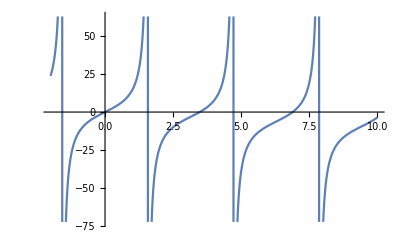

4.68409     348.635     2.41591

3.47614     -6.32637×10^-8     1.20795

2.87216     -5.6336     0.603977

3.17415     -2.84844     0.301988

3.32515     -1.46872     0.150994

3.40064     -0.750591     0.0754971

3.43839     -0.380066     0.0377485

3.45727     -0.191321     0.0188743

3.4667     -0.0959949     0.00943713

3.47142     -0.0480827     0.00471857

3.47378     -0.0240628     0.00235928

3.47496     -0.0120369     0.00117964

3.47555     -0.00601981     0.000589821

3.47585     -0.00301028     0.00029491

3.47599     -0.00150525     0.000147455

3.47607     -0.00075268     0.0000737276

3.4761     -0.000376377     0.0000368638

3.47612     -0.000188221     0.0000184319

3.47613     -0.0000941426     9.21595×10^-6

3.47614     -0.000047103     4.60798×10^-6

3.47614     -0.0000235832     2.30399×10^-6

3.47614     -0.0000118232     1.15199×10^-6

```mathematica
f[x_] = 10(Tan[x]) -x;
Plot[f[x], {x, -2, 10}]

a = 2.26818707; b = 7.1;
fa = f[a]; fb = f[b];
eps = .000001;
error = (b-a)/2.;

While[ Abs[error]>eps,
c = a+error;
fc = f[c];
Print[c, "     ",fc,"     ",error];
error = error/2;
If[fa fb> 0, a = c; fa = fb, b =c; fb = fc]]
```

```mathematica
(* newtons method *)
g[x_] = 10(Tan[x]) - x;
gp[x_] = g'[x];
Plot[g[x], {x,-2,10}]

For[i = 1; y = 4., i < 7, i++,
y = y - g[y]/gp[y];
Print[y,"    ",f[y]]]
```

-Graphics-

3.66177    2.0662

3.49353    0.17868

3.47626    0.00121535

3.47614    5.52315×10^-8

3.47614    -1.33227×10^-15

3.47614    -1.33227×10^-15

```mathematica
(* secant Method *)
h[x_] = 10(Tan[x]) - x;
Plot[h[x], {x, -2, 10}]

zo = -1.;
z= 4.;

For[i = 2, i < 12, i++,
zn = z - h[z]*(z-zo)/(h[z]-h[zo]);
Print[i,"    ",zn,"    ",h[zn]];
zo = z;
z = zn;]
```

-Graphics-

2    2.28952    -13.7206

3    3.3914    -0.840012

4    3.46326    -0.13083

5    3.47652    0.00386461

6    3.47614    -0.0000187728

7    3.47614    -2.713×10^-9

8    3.47614    3.10862×10^-15

9    3.47614    -1.33227×10^-15

10    3.47614    -1.33227×10^-15

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

11    Indeterminate    Indeterminate

```mathematica
(* false positives *)
f[x_] = 10(Tan[x]) -x;
Plot[f[x], {x, -2, 10}]

a = 2.; b = 4.;
fa = f[a]; fb = f[b];
c=((a*fb)-(b*fa))/(fb-fa);
fc = f[c];
k = 0;
m= 30;

While[ m>k,
If[Sign[f[b]]==Sign[f[c]], b= c, a =c;];
c=((a*fb)-(b*fa))/(fb-fa);
k = k+1;
Print[c, "     ",f[c],"     "];]
```

-Graphics-

3.15178     -3.04987

3.42951     -0.468079

3.49647     0.209217

3.48033     0.042796

3.46807     -0.0821115

3.47737     0.012571

3.47513     -0.0103203

3.47683     0.00704778

3.47642     0.00285784

3.47611     -0.000320916

3.47635     0.0020913

3.47629     0.00150961

3.47624     0.0010682

3.47621     0.00073324

3.47619     0.000479049

3.47617     0.000286154

3.47615     0.000139772

3.47614     0.0000286871

3.47613     -0.0000556117

3.47614     8.36052×10^-6

3.47614     -7.06479×10^-6

3.47614     4.64109×10^-6

3.47614     1.81852×10^-6

3.47614     -3.23467×10^-7

3.47614     1.30203×10^-6

3.47614     9.10084×10^-7

3.47614     6.12644×10^-7

3.47614     3.86925×10^-7

3.47614     2.15632×10^-7

3.47614     8.56416×10^-8